# Enhanced mixing in annular magneto-Stokes flow

Cy  S . David, Eric W. Hester, Yufan Xu, and Jonathan M. Aurnou

This notebook implements asymptotic predictions for the time required to mix a diffusing tracer in annular magneto-Stokes flow, a schematic for which is shown in Figure 1. The scaling laws used here are derived in Section 5.2 of “Magneto-Stokes flow in a shallow free-surface annulus” (David et al. 2024).

Figure 1. (a) Diagram of the magneto-Stokes system. A power supply controls the electric current I through the fluid layer. Radially outwards (+e_r) current density J and downwards (−e_z) magnetic field B produce an azimuthal (+e_θ) Lorentz force F on the fluid. (b) Photograph of a laboratory realization, with flow visualised by blue dye. The channel rests atop a wooden case of permanent magnets.

The goal of this notebook is to provide rough estimates of mixing efficiency over many orders of magnitude in the Peclet number (or electromagnetic forcing strength). Given constraints on the fluid/tracer properties and overall size of the channel, this tool may help practitioners determine the range of electromagnetic forcing needed to sufficiently enhance mixing. 

For a chosen set of parameters, 3-D numerical simulations should still be used to provide the most accurate mixing time predictions. This notebook’s asymptotic predictions at intermediate Peclet numbers (especially near the transition between Taylor dispersion and advection-dominated regimes) should be treated with particular caution, as discussed by David et al. (2024).

### Input parameters

Click on the gray bar below and press “Shift + Enter,” then change parameters as needed by adjusting the sliders or typing in the input boxes.

```mathematica
SetOptions[EvaluationNotebook[],CellProlog:>SelectionMove[NextCell[CellStyle->"Input"],All,Cell]]

(*DIFFUSION-DOMINATED REGIME*)
det[m_,ℛ_, λ_] =(D[BesselJ[m,λ r],r]//.{r->ℛ})(D[BesselY[m,λ r],r]//.{r->1})-(D[BesselJ[m,λ r],r]//.{r->1})(D[BesselY[m,λ r],r]//.{r->ℛ});
roots[m_,ℛ_,low_,upp_]:= Flatten[Values[{ToRules[Reduce[det[m,ℛ, λ]==0&&low<λ<upp,λ]]}]];

(*TAYLOR DISPERSION REGIME*)
u2Dmode[ρ_,ζ_,n_,ℋ_,ℛ_]=(16 (1+ℛ) (BesselI[1,((-1/2+n) π ρ)/ℋ] (-ρ BesselK[1,((-1/2+n) π)/ℋ]+ℛ ρ BesselK[1,((-1/2+n) π ℛ)/ℋ])+ℛ BesselI[1,((-1/2+n) π ℛ)/ℋ] (BesselK[1,((-1/2+n) π)/ℋ]-ρ BesselK[1,((-1/2+n) π ρ)/ℋ])+BesselI[1,((-1/2+n) π)/ℋ] (-ℛ BesselK[1,((-1/2+n) π ℛ)/ℋ]+ρ BesselK[1,((-1/2+n) π ρ)/ℋ])) Sin[(-1/2+n) π ζ])/((-1+2 n)^3 π^3 ℛ ρ (BesselI[1,((-1/2+n) π ℛ)/ℋ] BesselK[1,((-1/2+n) π)/ℋ]-BesselI[1,((-1/2+n) π)/ℋ] BesselK[1,((-1/2+n) π ℛ)/ℋ]));

u2DTrunc[ρ_,ζ_,ℋ_,ℛ_,p_]:=
Module[{n,u},
n=1;
u =If[(Quiet[Abs[u2Dmode[1,1,n,ℋ,ℛ ]]]<∞),u2Dmode[ρ,ζ,n,ℋ,ℛ],0];
n++;
While[(Quiet[Abs[u2Dmode[1,1,n,ℋ,ℛ ]]]<∞)&&(Quiet[Abs[(u2Dmode[(1+ℛ)/2,1,n,ℋ,ℛ ]+u2Dmode[(1+ℛ)/2,1,n+1,ℋ,ℛ ])/u2Dmode[(1+ℛ)/2,1,1,ℋ,ℛ]]]>10^-p),
u=u+u2Dmode[ρ,ζ,n,ℋ,ℛ];
n++
];
u
];

dudρTrunc[ρ_,ζ_,ℋ_,ℛ_,p_]:=
Module[{n,u},
n=1;
u =If[(Quiet[Abs[u2Dmode[1,1,n,ℋ,ℛ ]]]<∞),u2Dmode[ρ,ζ,n,ℋ,ℛ],0];
n++;
While[(Quiet[Abs[u2Dmode[1,1,n,ℋ,ℛ ]]]<∞)&&(Quiet[Abs[(u2Dmode[(1+ℛ)/2,1,n,ℋ,ℛ ]+u2Dmode[(1+ℛ)/2,1,n+1,ℋ,ℛ ])/u2Dmode[(1+ℛ)/2,1,1,ℋ,ℛ]]]>10^-p),
u=u+u2Dmode[ρ,ζ,n,ℋ,ℛ];
n++
];
D[u,ρ]
];

dudζTrunc[ρ_,ζ_,ℋ_,ℛ_,p_]:=
Module[{n,u},
n=1;
u =If[(Quiet[Abs[u2Dmode[1,1,n,ℋ,ℛ ]]]<∞),u2Dmode[ρ,ζ,n,ℋ,ℛ],0];
n++;
While[(Quiet[Abs[u2Dmode[1,1,n,ℋ,ℛ ]]]<∞)&&(Quiet[Abs[(u2Dmode[(1+ℛ)/2,1,n,ℋ,ℛ ]+u2Dmode[(1+ℛ)/2,1,n+1,ℋ,ℛ ])/u2Dmode[(1+ℛ)/2,1,1,ℋ,ℛ]]]>10^-p),
u=u+u2Dmode[ρ,ζ,n,ℋ,ℛ];
n++
];
D[u,ζ]
];

DispCoeff[ℋ_,ℛ_]:=
Module[{ω,ωb,f,PoissonEqn,Ka1solnC,Ka1Soln,Keffcoeff},
ω=u2DTrunc[ρ,ζ,ℋ,ℛ ,3]/ρ;
ωb=2/(1-ℛ^2)NIntegrate[ρ ω,{ρ,ℛ,1},{ζ,0,1}];
f =(1+ℛ)^2/2(ω-ωb);
PoissonEqn=ℋ^2(Derivative[2,0][Ka1][ρ,ζ]+(Derivative[1,0][Ka1][ρ,ζ])/ρ)+Derivative[0,2][Ka1][ρ,ζ]== f+NeumannValue[0,(ρ==ℛ)||(ρ==1)||(ζ==0)||(ζ==1)];
Off[NDSolveValue::femibcnd];
Ka1solnC =NDSolveValue[PoissonEqn,Ka1[ρ,ζ],{ρ,ℛ,1},{ζ,0,1}];
On[NDSolveValue::femibcnd];
Off[NIntegrate::slwcon];
Ka1Soln=(Ka1solnC -2/(1-ℛ^2)NIntegrate[ρ Ka1solnC,{ρ,ℛ,1},{ζ,0,1}]);
dispcoeff=(-(1+ℛ)^2)/2 2/(1-ℛ^2)NIntegrate[ρ Ka1Soln (ω-ωb),{ρ,ℛ,1},{ζ,0,1}];
On[NIntegrate::slwcon];
dispcoeff
];

(*ADVECTION-DOMINATED REGIME*)
gradomega2Trunc[ρ_,ζ_,ℋ_,ℛ_,p_]:=(dudζTrunc[ρ,ζ,ℋ,ℛ,p]/ρ)^2+ℋ^2(-u2DTrunc[ρ,ζ,ℋ,ℛ,p]/ρ^2+dudρTrunc[ρ,ζ,ℋ,ℛ,p]/ρ)^2

ro=None;
ri=None;
h=None;
nu=None;
varrho=None;
kappac=None;
MM=None;
R=None;
H=None;
gamma=None;

Manipulate[
ro = Quantity[outerradius,"Millimeters"];
ri = Quantity[innerradius,"Millimeters"];
h = Quantity[height,"Micrometers"];
nu = Quantity[viscosity,("Meters")^2/"Seconds"];
varrho = Quantity[density,"Kilograms"/("Meters")^3];
kappac = Quantity[diffusivity,("Centimeters")^2/"Seconds"];
MM=Mval;
R=(ri/ro)//N;
H=(h/ro)//N;
gamma=(h/(ro-ri))//N;
Row[{"Γ = h/(r_o-r_i) = ",gamma,",   R = r_i/r_o = ",R}],
{{outerradius,5,"outer radius, r_o (mm)"},5*10^-2,5*10^2,
Appearance->{"Open"}},
{{innerradius,4.5, "inner radius, r_i (mm)"},4.5*10^-2,outerradius,
Appearance->{"Open"}},
{{height,425, "fluid depth, h (μm)"},1000*0.12*(outerradius-innerradius),1000*6*(outerradius-innerradius),
Appearance->{"Open"}},
{{viscosity,10^-6//N,"viscosity, ν (m^2/s)"},10^-8,10^-4,
Appearance->{"Open"}},
{{density,10^3//N,"density, ϱ (kg/m^3)"},10^1,10^5,
Appearance->{"Open"}},
{{diffusivity,57*10^-8//N,"diffusivity, κ_c (m^2/s)"},57*10^-10,57*10^-6,
Appearance->{"Open"}},
{{Mval,0.3,"mixing norm, M"},0.1,0.7,
Appearance->{"Open"}}
]
```

### Predict mixing times

To compute and plot the mixing time predictions, click on the gray bar below and press “Shift + Enter.” Evaluation may take up to 4 minutes at Γ = 0.85, and takes longer at higher values of Γ.

Mouse over the plots to inspect specific values.

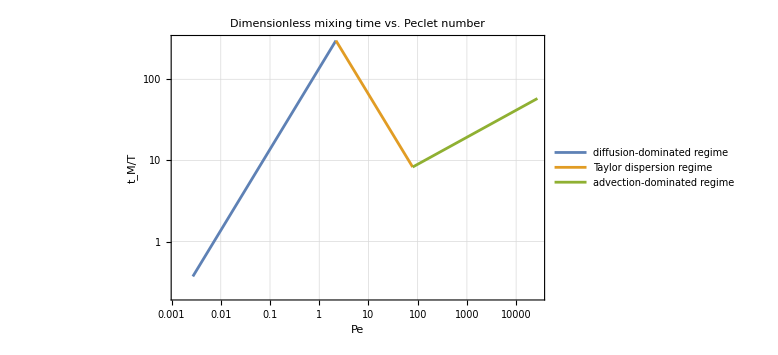

Note: T = (r_i+r_o)/U,  U = B_0hI_0/[2πνϱ(r_i+r_o)], Pe = h^2/(κ_cT).

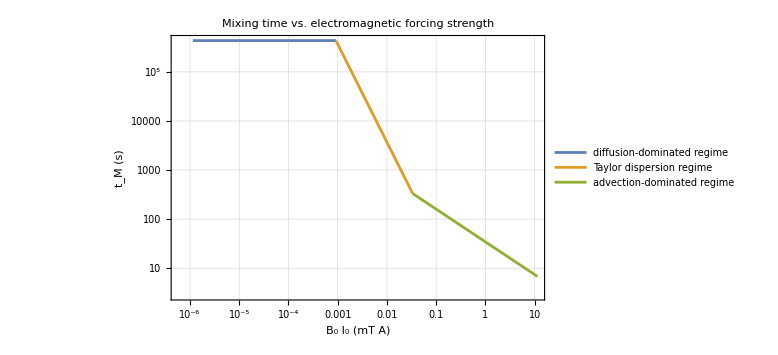

```mathematica
(*Diffusion-dominated regime*)
msg=PrintTemporary["Computing diffusion-dominated scaling..."];
lambda11 = Quiet[roots[1,R,0,10][[1]]];
tMDiffOverT[M_,pe_]=(1/(H^2 lambda11^2)Log[(2 √2)/(π M)]pe) ;
NotebookDelete[msg];
msg1=PrintTemporary["Computing diffusion-dominated scaling... Done."];

(*Taylor-dispersion regime*)
msg=PrintTemporary["Computing Taylor dispersion scaling..."];
tMTaylorDispOverT[M_,pe_]=((1+R)^2/(4 DispCoeff[H,R])Log[(2 √2)/(π M)] pe^-1) ;
Pe0 = (lambda11 H(1+R))/(2 Sqrt[DispCoeff[H,R] ]);
NotebookDelete[msg];
msg2=PrintTemporary["Computing Taylor dispersion scaling... Done."];

(*Advection-dominated regime*)
msg=PrintTemporary["Computing advection-dominated scaling..."];
FNintegrand[τp_,ρp_,ζp_]=ⅇ^(-2/3 (1+R)^2 τp^3 gradomega2Trunc[ρp,ζp,H,R,3])ρp;
FN[τp_]:=Module[{FNInteg},
FNInteg[ρp_,ζp_]=Evaluate[FNintegrand[τp,ρp,ζp]];

(2/(1-R^2)NIntegrate[FNInteg[ρp,ζp],{ρp,R,1},{ζp,0,1}])^(1/2)];
mN[τp_]:=(2 √2)/π FN[τp];
Off[NIntegrate::slwcon];
τpStart=0.05;
mStart=mN[τpStart];
While[mStart<0.5,
τpStart =τpStart/2;
mStart=mN[τpStart];
];
τpEnd=5;
mEnd=mN[τpEnd];
While[mEnd>0.01,
τpEnd =2*τpEnd;
mEnd=mN[τpEnd];
];
Nevalpts=25;
τpList=Table[τpStart(τpEnd/τpStart)^((i-1)/(Nevalpts-1)),{i,1,Nevalpts}];
evalpts=Monitor[Table[{τpList[[i]],mN[τpList[[i]]]},{i,1,Length[τpList]}],ProgressIndicator[i,{1,Length[τpList]}]];
On[NIntegrate::slwcon];
mNInterp[τp_]=Exp[Interpolation[Table[{evalpts[[i]][[1]],Log[evalpts[[i]][[2]]]},{i,1,Length[evalpts]}]][τp]];
τpInterp[M_]:=Quiet[τp//.FindRoot[mNInterp[τp]==M,{τp,τpList[[Length[τpList]-1]]}]];
tMAdvecOverT[M_,pe_]:=(τpInterp[M] pe^(1/3)) ;
PeTDAdv[M_]:=((1+R)^(3/2) Log[(2 √2)/(M π)]^(3/4))/(2 √2 DispCoeff[H,R]^(3/4) τpInterp[M]^(3/4));
NotebookDelete[msg];
msg3=PrintTemporary["Computing advection-dominated scaling... Done."];
NotebookDelete[msg1];
NotebookDelete[msg2];
NotebookDelete[msg3];

(*Plotting*)
msg=PrintTemporary["Plotting..."];
PeTildeLow=10^2;
PeTildeHigh = 10^9;
PeLow = PeTildeLow/(2Pi(1+R)^2/H^3);
PeHigh=PeTildeHigh/(2Pi(1+R)^2/H^3);
PeDiffList=10^Range[Log10[PeLow],Log10[Pe0],(Log10[Pe0]-Log10[PeLow])/99];
PeTildeDiffList=(2Pi(1+R)^2/H^3)*PeDiffList;
PeTDList=10^Range[Log10[Pe0],Log10[PeTDAdv[MM]],(Log10[PeTDAdv[MM]]-Log10[Pe0])/99];
PeTildeTDList=(2Pi(1+R)^2/H^3)*PeTDList;
PeAdvList=10^Range[Log10[PeTDAdv[MM]],Log10[PeHigh],(Log10[PeHigh]-Log10[PeTDAdv[MM]])/99];
PeTildeAdvList=(2Pi(1+R)^2/H^3)*PeAdvList;


ListPlot[
{
Table[{PeDiffList[[i]],tMDiffOverT[MM,PeDiffList][[i]]},{i,1,Length[PeDiffList]}],
Table[{PeTDList[[i]],tMTaylorDispOverT[MM,PeTDList][[i]]},{i,1,Length[PeTDList]}],
Table[{PeAdvList[[i]],tMAdvecOverT[MM,PeAdvList][[i]]},{i,1,Length[PeAdvList]}]
},
PlotLegends->{"diffusion-dominated regime","Taylor dispersion regime","advection-dominated regime"},
ScalingFunctions->{"Log","Log"},
Joined->True,
PlotRange->All,
Frame->True,
FrameLabel->{"Pe","t_M/T"},
GridLines->Automatic,
PlotLabel->"Dimensionless mixing time vs. Peclet number",
ImageSize->Large
]

Print["Note: T = (r_i+r_o)/U,  U = B_0hI_0/[2πνϱ(r_i+r_o)], Pe = h^2/(κ_cT)."]
Print["\n"]

ListPlot[
{
Table[{UnitConvert[varrho nu kappac/ro,"Amperes"*"Milliteslas"]PeTildeDiffList[[i]],(ro^2/kappac H^2/PeDiffList tMDiffOverT[MM,PeDiffList])[[i]]},{i,1,Length[PeDiffList]}],Table[{UnitConvert[varrho nu kappac/ro,"Amperes"*"Milliteslas"]PeTildeTDList[[i]],(ro^2/kappac H^2/PeTDList tMTaylorDispOverT[MM,PeTDList])[[i]]},{i,1,Length[PeTDList]}],
Table[{UnitConvert[varrho nu kappac/ro,"Amperes"*"Milliteslas"]PeTildeAdvList[[i]],(ro^2/kappac H^2/PeAdvList tMAdvecOverT[MM,PeAdvList])[[i]]},{i,1,Length[PeAdvList]}]
},
PlotLegends->{"diffusion-dominated regime","Taylor dispersion regime","advection-dominated regime"},
ScalingFunctions->{"Log","Log"},
Joined->True,
GridLines->Automatic,
PlotRange->All,
Frame->True,
FrameLabel->{"B_0 I_0 (mT A)","t_M (s)"},
PlotLabel->"Mixing time vs. electromagnetic forcing strength",
ImageSize->Large]
NotebookDelete[msg];
```